# Finding Energy Levels

## Setting B Field

```mathematica
BField=175;
```

## Constants (not the only section)

```mathematica
ℏc=197.326968;
cLight=2.99792458*10^17;
ℏPlank=2 π ℏc/cLight;
μBohr=5.788381804*10^-5;
μe=1.0011596521859 μBohr;

Ehf=3.036*10^9 ℏPlank;
Bhf=Ehf/μe 10^4;
ρB=2*BField/Bhf;

m=84.911789738×931.494028×10^6;
μ=m/2;
ℏ=197.3269631;

αfsc=1/137.035999070;
a0=5.2917720859×10^-2;

Hartree=(αfsc*ℏc)/a0;
```

## Getting Data

```mathematica
potFile="/home/cnewby/SeniorDesign/Stuff/Rbpots.dat";
potList=ReadList[potFile,{Number,Number,Number}];
Np=Length[potList];len=Np;

rList=Table[potList[[i,1]],{i,1,Np}];
VsList=Table[potList[[i,2]],{i,1,Np}];
VtList=Table[potList[[i,3]],{i,1,Np}];

VsDataList=Table[{rList[[i]],VsList[[i]]},{i,1,Np}];
VtDataList=Table[{rList[[i]],VtList[[i]]},{i,1,Np}];

Vs=VsDataList;
Vt=VtDataList;
```

## Getting Matrix Elements for the Channels

### Setting Constants

```mathematica
ℏc=197.326968;
cLight=2.99792458*10^17;
ℏPlank=2 π ℏc/cLight;
μBohr=5.788381804*10^-5;
μe=1.0011596521859 μBohr;

Ehf=3.036*10^9 ℏPlank;
Bhf=Ehf/μe 10^4;
ρB=2*BField/Bhf;

Print["ρB for ",BField," gauss is ",ρB]
```

ρB for 175 gauss is 0.16154

### Hyperfine and Zeeman Splitting

```mathematica
Hhf[i_,s_,f_]:=(f (f+1)-i (i+1)-s (s+1))/(2 i+1);

Sz[i_,s_,finit_,m_,ffin_]:=Sqrt[3]/2 (-1)^(ffin+s+i+1) Sqrt[(2 s+1) (2 finit+1)]SixJSymbol[{i,s,finit},{1,ffin,s}]ClebschGordan[{finit,m},{1,0},{ffin,m}];
```

### Single Atom Stuff

```mathematica
H33=Hhf[5/2,1/2,3]+ρB*Sz[5/2,1/2,3,-3,3];
Hm3={{0,0},{0,H33}};
e3=Eigenvalues[Hm3];

H22=Hhf[5/2,1/2,2]+ρB*Sz[5/2,1/2,2,-2,2];
H23=ρB*Sz[5/2,1/2,2,-2,3];
H32=H23;
H33=Hhf[5/2,1/2,3]+ρB*Sz[5/2,1/2,3,-2,3];
Hm2={{H22,H23},{H32,H33}};
C3=H23;
C2=(H22-H33)/2;
θ2=ArcTan[C3/C2];
e2=Eigenvalues[Hm2];

H22=Hhf[5/2,1/2,2]+ρB*Sz[5/2,1/2,2,-1,2];
H23=ρB*Sz[5/2,1/2,2,-1,3];
H32=H23;
H33=Hhf[5/2,1/2,3]+ρB*Sz[5/2,1/2,3,-1,3];
Hm1={{H22,H23},{H32,H33}};
C3=H23;
C2=(H22-H33)/2;
θ1=ArcTan[C3/C2];
e1=Eigenvalues[Hm1];

Print["H for m=-3 = ",Hm3//MatrixForm]
Print["Eigenvalues and Eigenvectors = ",Eigensystem[Hm3],"\n\n"]

Print["H for m=-2 = ",Hm2//MatrixForm]
Print["Eigenvalues and Eigenvectors = ",Eigensystem[Hm2]]
Print["θ2 = ",θ2,"\n\n"]

Print["H for m=-1 = ",Hm1//MatrixForm]
Print["Eigenvalues and Eigenvectors = ",Eigensystem[Hm1]]
Print["θ1 = ",θ1,"\n\n"]
```

H for m=-3 = (0 | 0
0 | 0.335896)

Eigenvalues and Eigenvectors = {{0.335896,0.},{{0.,1.},{1.,0.}}}

H for m=-2 = (-0.529487 | -0.0602026
-0.0602026 | 0.36282)

Eigenvalues and Eigenvectors = {{-0.53353,0.366863},{{0.997752,0.0670131},{-0.0670131,0.997752}}}

θ2 = 0.134127

H for m=-1 = (-0.55641 | -0.0761509
-0.0761509 | 0.389743)

Eigenvalues and Eigenvectors = {{-0.5625,0.395833},{{0.996818,0.0797155},{-0.0797155,0.996818}}}

θ1 = 0.1596

### Two Atom Mixing

```mathematica
Ebot=e2[[1]]+e2[[1]]
Δo=e2[[1]]+e2[[1]]-Ebot;
Δa=e3[[1]]+e1[[1]]-Ebot;
Δb=e2[[1]]+e2[[2]]-Ebot;
Δc=e3[[1]]+e1[[2]]-Ebot;
Δd=e2[[2]]+e2[[2]]-Ebot;
{Δo,Δa,Δb,Δc,Δd}//MatrixForm
```

-1.06706

(0.
0.840457
0.900393
1.79879
1.80079)

### Atom-Atom Interaction

```mathematica
Aa=ClebschGordan[{5/2,-5/2},{1/2,1/2},{2,-2}];
Bb=ClebschGordan[{5/2,-3/2},{1/2,-1/2},{2,-2}];
Cc=ClebschGordan[{5/2,-5/2},{1/2,1/2},{3,-2}];
Dd=ClebschGordan[{5/2,-3/2},{1/2,-1/2},{3,-2}];
Ee=ClebschGordan[{5/2,-3/2},{1/2,1/2},{2,-1}];
Ff=ClebschGordan[{5/2,-1/2},{1/2,-1/2},{2,-1}];
Gg=ClebschGordan[{5/2,-5/2},{1/2,-1/2},{3,-3}];
Hh=ClebschGordan[{5/2,-3/2},{1/2,1/2},{3,-1}];
Ii=ClebschGordan[{5/2,-1/2},{1/2,-1/2},{3,-1}];
Ss=ClebschGordan[{1/2,1/2},{1/2,-1/2},{0,0}];

S1=ClebschGordan[{1/2,1/2},{1/2,-1/2},{0,0}];
S2=ClebschGordan[{1/2,-1/2},{1/2,1/2},{0,0}];

Jj=ClebschGordan[{5/2,-5/2},{5/2,-3/2},{4,-4}];
Kk=ClebschGordan[{5/2,-5/2},{5/2,-3/2},{5,-4}];
Ll=ClebschGordan[{5/2,-3/2},{5/2,-5/2},{4,-4}];
Mm=ClebschGordan[{5/2,-3/2},{5/2,-5/2},{5,-4}];

OChan=(2 Cos[θ2/2]^2 Aa Bb Ss+2 Cos[θ2/2] Sin[θ2/2] Ss (Aa Dd+Cc Bb)+2 Sin[θ2/2]^2 Cc Dd Ss) Jj;
aChan=Cos[θ1/2] Ee Gg Ss+Sin[θ1/2] Hh Gg Ss;
bChan=-(2/Sqrt[2]) ((S1 Jj Aa Dd+S2 Ll Bb Cc)*(Cos[θ2/2]^2-Sin[θ2/2]^2)-(S1 Jj+S2 Ll)*2 (Sin[θ2/2] Cos[θ2/2] Aa Cc));
cChan=-Cos[θ1/2] Hh Gg Ss+Sin[θ1/2] Ee Gg Ss;
dChan=(2 Cos[θ2/2]^2 Cc Dd Ss-2 Cos[θ2/2] Sin[θ2/2] Ss (Aa Dd+Cc Bb)+2 Sin[θ2/2]^2 Aa Bb Ss) Jj;

P11=OChan^2;
P22=aChan^2;
P33=bChan^2;
P44=cChan^2;
P55=dChan^2;

P21=OChan*aChan;P12=P21;
P31=OChan*bChan;P13=P31;
P41=OChan*cChan;P14=P41;
P51=OChan*dChan;P15=P51;
P32=aChan*bChan;P23=P32;
P42=aChan*cChan;P24=P42;
P52=aChan*dChan;P25=P52;
P43=bChan*cChan;P34=P43;
P53=bChan*dChan;P35=P53;
P54=cChan*dChan;P45=P54;
Ps={{P11,P12,P13,P14,P15},{P21,P22,P23,P24,P25},{P31,P32,P33,P34,P35},{P41,P42,P43,P44,P45},{P51,P52,P53,P54,P55}};
Ps//MatrixForm
Pt=IdentityMatrix[5]-Ps;
Pt//MatrixForm
```

(0.171318 | -0.224738 | -0.164193 | -0.187488 | -0.171318
-0.224738 | 0.294816 | 0.215391 | 0.24595 | 0.224738
-0.164193 | 0.215391 | 0.157364 | 0.17969 | 0.164193
-0.187488 | 0.24595 | 0.17969 | 0.205184 | 0.187488
-0.171318 | 0.224738 | 0.164193 | 0.187488 | 0.171318)

(0.828682 | 0.224738 | 0.164193 | 0.187488 | 0.171318
0.224738 | 0.705184 | -0.215391 | -0.24595 | -0.224738
0.164193 | -0.215391 | 0.842636 | -0.17969 | -0.164193
0.187488 | -0.24595 | -0.17969 | 0.794816 | -0.187488
0.171318 | -0.224738 | -0.164193 | -0.187488 | 0.828682)

## Channel Plots

### With Δ added in

```mathematica
Vopen=Table[{Vs⟦i,1⟧,Vs⟦i,2⟧*Ps⟦1,1⟧+Vt⟦i,2⟧*Pt⟦1,1⟧+Δo*Ehf},{i,1,len}];

Va=Table[{Vs⟦i,1⟧,Vs⟦i,2⟧*Ps⟦2,2⟧+Vt⟦i,2⟧*Pt⟦2,2⟧+Δa*Ehf},{i,1,len}];

Vb=Table[{Vs⟦i,1⟧,Vs⟦i,2⟧*Ps⟦3,3⟧+Vt⟦i,2⟧*Pt⟦3,3⟧+Δb*Ehf},{i,1,len}];

Vc=Table[{Vs⟦i,1⟧,Vs⟦i,2⟧*Ps⟦4,4⟧+Vt⟦i,2⟧*Pt⟦4,4⟧+Δc*Ehf},{i,1,len}];

Vd=Table[{Vs⟦i,1⟧,Vs⟦i,2⟧*Ps⟦5,5⟧+Vt⟦i,2⟧*Pt⟦5,5⟧+Δd*Ehf},{i,1,len}];
```

```mathematica
VopenPlot=ListPlot[Vopen,Joined->True,PlotStyle->{Thickness[.00175],Blue},PlotRange->{{0,2},{-6 10^-1,6 10^-1}}];
VaPlot=ListPlot[Va,Joined->True,PlotStyle->Red,PlotRange->{{0,2},{-6 10^-1,6 10^-1}}];
VbPlot=ListPlot[Vb,Joined->True,PlotStyle->Green,PlotRange->{{0,2},{-6 10^-1,6 10^-1}}];
VcPlot=ListPlot[Vc,Joined->True,PlotStyle->Orange,PlotRange->{{0,2},{-6 10^-1,6 10^-1}}];
VdPlot=ListPlot[Vd,Joined->True,PlotStyle->Purple,PlotRange->{{0,2},{-6 10^-1,6 10^-1}}];

aA=ListPlot[{{.8,10}},PlotMarkers->"Open Channel",PlotStyle->Blue];
bB=ListPlot[{{.8,9}},PlotMarkers->"Channel a",PlotStyle->Red];
cC=ListPlot[{{.8,8}},PlotMarkers->"Channel b",PlotStyle->Green];
dD=ListPlot[{{.8,7}},PlotMarkers->"Channel c",PlotStyle->Orange];
eE=ListPlot[{{.8,6}},PlotMarkers->"Channel d",PlotStyle->Purple];
fF=ListPlot[{{.7,11},{.9,11},{.9,5},{.7,5},{.7,11}},PlotStyle->{Black,Thick},Joined->True];
```

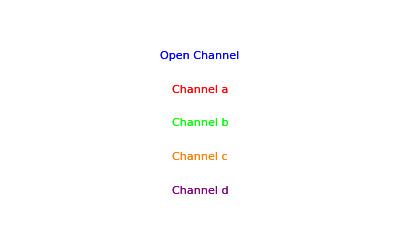

```mathematica
graph3=Show[aA,bB,cC,dD,eE,Axes->False,PlotRange->{{.7,.9},{5,11}}]
```

```mathematica
VopenN=Table[{Vs⟦i,1⟧,(Vs⟦i,2⟧*Ps⟦1,1⟧+Vt⟦i,2⟧*Pt⟦1,1⟧+Δo*Ehf)*1000},{i,1,len}];

VaN=Table[{Vs⟦i,1⟧,(Vs⟦i,2⟧*Ps⟦2,2⟧+Vt⟦i,2⟧*Pt⟦2,2⟧+Δa*Ehf)*1000},{i,1,len}];

VbN=Table[{Vs⟦i,1⟧,(Vs⟦i,2⟧*Ps⟦3,3⟧+Vt⟦i,2⟧*Pt⟦3,3⟧+Δb*Ehf)*1000},{i,1,len}];

VcN=Table[{Vs⟦i,1⟧,(Vs⟦i,2⟧*Ps⟦4,4⟧+Vt⟦i,2⟧*Pt⟦4,4⟧+Δc*Ehf)*1000},{i,1,len}];

VdN=Table[{Vs⟦i,1⟧,(Vs⟦i,2⟧*Ps⟦5,5⟧+Vt⟦i,2⟧*Pt⟦5,5⟧+Δd*Ehf)*1000},{i,1,len}];
```

```mathematica
VopenPlotN=ListPlot[VopenN,Joined->True,PlotStyle->{Thick,Blue},PlotRange->{{0,2},{-6 10^-1,6 10^-1}}];
VaPlotN=ListPlot[VaN,Joined->True,PlotStyle->Red,PlotRange->{{0,2},{-6 10^-1,6 10^-1}}];
VbPlotN=ListPlot[VbN,Joined->True,PlotStyle->Green,PlotRange->{{0,2},{-6 10^-1,6 10^-1}}];
VcPlotN=ListPlot[VcN,Joined->True,PlotStyle->Orange,PlotRange->{{0,2},{-6 10^-1,6 10^-1}}];
VdPlotN=ListPlot[VdN,Joined->True,PlotStyle->Purple,PlotRange->{{0,2},{-6 10^-1,6 10^-1}}];

aA=ListPlot[{{9.05,.000001}},PlotMarkers->"Open Channel",PlotStyle->Blue];
bB=ListPlot[{{9.05,.000009}},PlotMarkers->"Channel a",PlotStyle->Red];
cC=ListPlot[{{9.05,.0000125}},PlotMarkers->"Channel b",PlotStyle->Green];
dD=ListPlot[{{9.05,.0000212}},PlotMarkers->"Channel c",PlotStyle->Orange];
eE=ListPlot[{{9.05,0.0000237}},PlotMarkers->"Channel d",PlotStyle->Purple];

graph2=Show[VopenPlotN,VaPlotN,VbPlotN,VcPlotN,VdPlotN,(*aA,bB,cC,dD,eE,*)PlotRange->{{9,9.1},{-.0000002*1000,.000025*1000}},AxesLabel->{"r (nm)","V(r) (meV)"},Ticks->{{9.0,9.05,9.1},{0.0,0.01,0.02}}]
```

-Graphics-

```mathematica
graph=Show[VopenPlot,VaPlot,VbPlot,VcPlot,VdPlot,PlotRange->{{0.2,1.37},{-.15,.3}},PlotLabel->"Channel Potentials with Separations",AxesLabel->{"r (nm)","V(r) (eV)"},Epilog->{Inset[graph2,{1.02,.15},Automatic,{.7,.7}],Inset[graph3,{.55,.15}]}]
```

-Graphics-

```mathematica
Export["/home/cnewby/SeniorDesign/Racah Sections/ChannelPotswithSep.eps",graph]
```

/home/cnewby/SeniorDesign/Racah Sections/ChannelPotswithSep.eps

```mathematica
Export["/home/cnewby/Desktop/csm-thesis/Figures/ChannelPotswithSepZoom.pdf",graph2]
```

/home/cnewby/Desktop/csm-thesis/Figures/ChannelPotswithSepZoom.pdf